```mathematica
findConvexHullCoordsConvexPolysAS[polyObstacle_,polyRobot_]:=Module[{pts},
(* this function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Jan 2, 2019*)
(*First, place the robot at each vertix of the obstacle, and record the vertices coordinates, then flatten this list*)
pts =Flatten[ Table[polyObstacle⟦1,i⟧- polyRobot⟦1,j⟧,{i,1,Length[polyObstacle⟦1⟧]},{j,1,Length[polyRobot⟦1⟧]}],1];
(*second, grab an ordered list of convex hull of these points*)#["Coordinates"][[#["BoundaryVertices"]⟦1⟧]]&@ConvexHullMesh[pts]
]
(*winding[] and testpoint[] from https://mathematica.stackexchange.com/questions/9405/how-to-check-if-a-2d-point-is-in-a-polygon *)
winding[poly_,pt_]:=Round[(Total@Mod[(#-RotateRight[#])&@(ArcTan@@(pt-#)&/@poly),2 Pi,-Pi]/2/Pi)]

(*true if pt  is inside polygon*)
(*https://mathematica.stackexchange.com/questions/9405/how-to-check-if-a-2d-point-is-in-a-polygon*)
testpoint[poly_,pt_]:=Round[(Total@Mod[(#-RotateRight[#])&@(ArcTan@@(pt-#)&/@poly),2 Pi,-Pi]/2/Pi)]≠0
```

```mathematica
linelineInt[{{x1_,y1_},{x2_,y2_}},{{x3_,y3_},{x4_,y4_}}]:=
(*Returns the Intersection Point between two lines.  Line A is from point 1 to 2, and line B is from point 3 to 4. Code from https://en.wikipedia.org/wiki/Line%E2%80%93line_intersection*)
{((x1 y2-y1 x2)(x3-x4)-(x1-x2)(x3 y4 -y3 x4))/((x1-x2)(y3-y4)-(y1-y2)(x3-x4)),
((x1 y2-y1 x2)(y3-y4)-(y1-y2)(x3 y4 -y3 x4))/((x1-x2)(y3-y4)-(y1-y2)(x3-x4))}
```

#### Too slow, but we can fix: 0.) Use a Module inside the manipulate to compartmentalize all your local variables. Manipulate[Module[{all your local variables}, rest of code], controls] 1.) make three sets of graph lines (blue lines), those only between configuration space obstacles, those only from start config, those only from end config. Store these as a control of type ‘none’ 2.) only update the graph lines if the corresponding node moves 3.) calculate the shortest path, color red. Only update if something changes 4.) make function isInPoly[], and color a configuration space obstacle (or the obstacle) bright red if the robot touches it: https://mathematica.stackexchange.com/questions/9405/how-to-check-if-a-2d-point-is-in-a-polygon 5.) make a slider for ‘progress’ that moves the robot from the start configuration to the goal configuration 6.) I think LaValle has some ideas about which of the blue lines can be removed. This will make the graphics cleaner, and make the code run faster: http://planning.cs.uiuc.edu/node271.html 7.) must make Minkowski of border (shrink workspace when in configuration space) 8.) force initial and final positions to be inside border 9.) clean up the [[ to ⟦ 10.) line from start to goal (if possible)

```mathematica
And@@{True,True,False}
```

False

```mathematica
Manipulate[
Module[{o,r,borderpoly,robotStartPoly,robotEndPoly,obstaclepoly,robotobstconfig,robotobstconfigPoly,lengthofrobotobstconfig,linesStarttoObstacles,linesEndtoObstacles,verticestoVertices,robotinsideobstcond,borderpolyA,boundMidpts,boundNormal,boundaryOffsets,configBoundary,obstCollision},
(*Locator array for object & robot(start & end)*)
o={o1,o2(*,o3,o4*)};
r={r1,r2};
borderpoly =10CirclePoints[x];
robotStartPoly = Polygon[(r⟦1⟧+ #)&/@CirclePoints[n]];
robotEndPoly = Polygon[(r⟦2⟧+ #)&/@CirclePoints[n]];
obstaclepoly=Table[Polygon[(o⟦i-3⟧+ #)&/@CirclePoints[i]],{i,4,3+Length[o],1}];

(*get the Minkowski sum between all obstacles & the robot*)
robotobstconfig=Table[(r⟦1⟧+ #)&/@findConvexHullCoordsConvexPolysAS[obstaclepoly⟦i⟧,robotStartPoly],{i,1,Length[obstaclepoly],1}];

robotobstconfigPoly=Polygon[robotobstconfig];
lengthofrobotobstconfig = Length[robotobstconfig];

(*Create Lines from Start Centroid to Minkowski Region Vertices which are not intersecting*)

(*linesStarttoObstacles = Table[Table[If[!Graphics`Mesh`IntersectQ[{lineStart=Line[{r⟦1⟧,robotobstconfig⟦j,i⟧}],robotobstconfigPoly}],lineStart],{i,1,Length[robotobstconfig⟦j⟧],1}],{j,1,lengthofrobotobstconfig,1}];

linesEndtoObstacles = Table[Table[If[!Graphics`Mesh`IntersectQ[{lineEnd=Line[{r⟦2⟧,robotobstconfig⟦j,i⟧}],robotobstconfigPoly}],lineEnd],{i,1,Length[robotobstconfig⟦j⟧],1}],{j,1,lengthofrobotobstconfig,1}];

(*Create Lines from End Centroid to Minkowski Region Vertices which are not intersecting*)

(*Create Lines from Vertice of Centroid to Minkowski Region to other Vertices which are not intersecting*)
verticestoVertices = 
Table[Table[Table[Table[If[!Graphics`Mesh`IntersectQ[{lineVertice=Line[{robotobstconfig⟦l,i⟧,robotobstconfig⟦k,j⟧}],robotobstconfigPoly}],lineVertice],
{i,1,Length[robotobstconfig⟦l⟧],1}],
{j,1,Length[robotobstconfig⟦k⟧],1}],
{k,1+l,lengthofrobotobstconfig,1}],
{l,1,lengthofrobotobstconfig,1}];*)

(*Compute the configuration space defined by the outer boundary.*)
borderpolyA = Append[borderpoly,borderpoly⟦1⟧];
boundMidpts = Table[(borderpolyA⟦i⟧+borderpolyA⟦i+1⟧)/2,{i,1,Length[borderpoly]}];
boundNormal = Table[Normalize[{borderpolyA⟦i+1,2⟧-borderpolyA⟦i,2⟧,borderpolyA⟦i,1⟧-borderpolyA⟦i+1,1⟧}],{i,1,Length[borderpoly]}];
boundaryOffsets = Table[First[MaximalBy[(#-r⟦1⟧)&/@robotStartPoly⟦1⟧, N[Dot[boundNormal⟦i⟧,#]]&]],{i,1,Length[borderpoly]}];
configBoundary = Table[ip1 = If[i<Length[borderpoly],i+1,1];
linelineInt[{borderpoly⟦i⟧-boundaryOffsets⟦i⟧,boundMidpts⟦i⟧-boundaryOffsets⟦i⟧},{borderpoly⟦ip1⟧-boundaryOffsets⟦ip1⟧,boundMidpts⟦ip1⟧-boundaryOffsets⟦ip1⟧}],{i,1,Length[borderpoly]}]; (*END Compute the configuration space defined by the outer boundary.*)


(*Get True or false if centroid of robot (start or end) is inside or outside of any obstacle and the boundry*)
(*robotinsideobstcond = Table[MemberQ[Append[(RegionMember[#,r⟦i⟧]&/@(Polygon[#]&/@robotobstconfig)),(!RegionMember[Polygon[configBoundary],r⟦i⟧])]
,True],{i,1,Length[r],1}];*)
obstCollision = Table[Table[testpoint[robotobstconfig⟦i⟧,r⟦j⟧],{i,1,Length[robotobstconfig]}],{j,1,Length[r]}];
robotinsideobstcond =Table[Or[!testpoint[configBoundary,r⟦j⟧],Or@@obstCollision⟦j⟧],{j,1,Length[r]}];

Graphics[{
White,Rectangle[10{-1,-1},10{1,1}],
EdgeForm[{Thin}],
(*Boundary Polygon*)
If[configOrWork=="work"
,{LightYellow,Polygon[ borderpoly]}
,{LightGray,Opacity[0.5],EdgeForm[{Pink}],Polygon[configBoundary],White,Opacity[1], 
Table[{If[Or[obstCollision⟦1,i⟧,obstCollision⟦2,i⟧],Red,White],Polygon[robotobstconfig⟦i⟧]},{i,1,Length[robotobstconfig]}]}
]
(*Direct Line from Start to Goal*)
,{Green,Opacity[0.5],Line[{r}]}
(*(*Lines from Start Centroid to Object Minkowski Space Vertices*)
,{Orange,Opacity[0.5],linesStarttoObstacles}
(*Lines from End Centroid to Object Minkowski Space Vertices*)
,{Purple,Opacity[0.5],linesEndtoObstacles}
(*Lines from Vertices of obstacles to other Minkowski Space Vertices*)
,{Blue,Opacity[0.5],verticestoVertices}*)

,If[configOrWork=="work",
(*Robot Start*)
{
If[robotinsideobstcond⟦1⟧,{Red, robotStartPoly}
,{LightBlue, robotStartPoly}]
(*Robot End*)
,If[robotinsideobstcond⟦2⟧,{Red, robotEndPoly}
,{LightGreen, robotEndPoly}]
,{LightRed,obstaclepoly}}]
(*Configuration Space of Robot & Obstacles*)
,{Red,PointSize[0.005],Point[Flatten[robotobstconfig,1]]}
,{Gray,Opacity[0.7],Line[robotobstconfig]}
}]]
(*Polygon Shape Slider*)
,{{configOrWork,"work","Space"},{"work","config"}},{n,3,10,1} ,{x,4,9,1} 
(*,{verticestoVertices,{{0,0},{0,1}},ControlType->None}
,{oldLocatorsO,{{-4,-5},{0,0}},ControlType->None}*)
(* Intial Robot Locator Position*)
,{{r1,{-4,6}},10{-1,-1},10{1,1},Locator}
,{{r2,{5,-5}},10{-1,-1},10{1,1},Locator} 
,{{o1,{4,5}},10{-1,-1},10{1,1},Locator}
,{{o2,{0,2}},10{-1,-1},10{1,1},Locator}
(*,{{o3,{-3,-4}},10{-1,-1},10{1,1},Locator}
,{{o4,{3,-3}},10{-1,-1},10{1,1},Locator}*)
,ContentSize->{380,380}
]
```

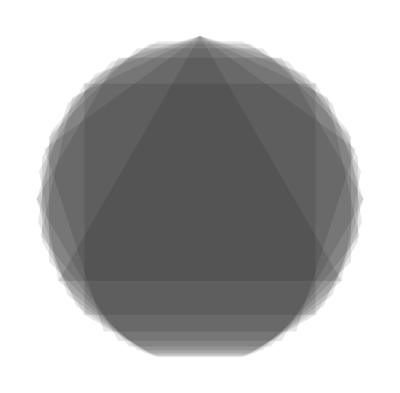

```mathematica
Graphics[{Opacity[0.1],Table[Polygon[CirclePoints[i]],{i,3,12}]}]
```

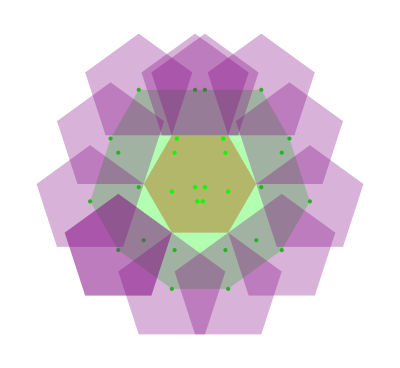

```mathematica
region1=Polygon[CirclePoints[6]];
robot=Polygon[CirclePoints[5]];
Graphics[{
Opacity[0.4],
Red,region1,
(*Blue,robot,*)
Opacity[1],Green,


(*find the coordinates of the convex hull:*)

pts =Flatten[Table[ Table[region1⟦1,i⟧-robot⟦1,j⟧,{i,1,Length[region1⟦1⟧]}],{j,1,Length[robot⟦1⟧]}],1];cvhullPt=#["Coordinates"][[#["BoundaryVertices"]⟦1⟧]]&@ConvexHullMesh[pts];
Point[pts],

Opacity[0.3],
Polygon[findConvexHullCoordsConvexPolysAS[region1,robot]],
(* draw the robot at the corners of the convex hull*)
Purple,
Table[Polygon[cvhullPt⟦i⟧+#&/@ robot⟦1⟧],{i,1,Length[cvhullPt]}]
}]
```

```mathematica
(*Does Not Work*)islineintersectingpoly[line_,polyobst_]:=Module[{dimension},
dimension= RegionDimension[DiscretizeRegion@RegionIntersection[polyobst,line]];
Return[dimension]
]
```

```mathematica
(*Test to Get True or false if centroid of robot (start or end) is inside of any obstacle*)
MemberQ[((RegionMember[#,r⟦1⟧])&/@(Polygon[#]&/@robotobstconfig)),True]
```

```mathematica
Append[Polygon[#]&/@robotobstconfig,Polygon[borderpoly]];
```

```mathematica
MemberQ[Append[(RegionMember[#,r⟦1⟧]&/@(Polygon[#]&/@robotobstconfig)),(!RegionMember[Polygon[borderpoly],r⟦1⟧])]
,True]
```

Graphics`Mesh`IntersectQ::ngdim1: Graphics primitives with coordinates {{-4.1,4.62},{-4.1+Polygon[{{4.70711,4.29289},{4.70711,5.70711},{3.29289,5.70711},{3.29289,4.29289}}],4.62+Polygon[{«1»}]}} are not supported.

Graphics`Mesh`IntersectQ::ngdim1: Graphics primitives with coordinates {{-4.1,4.62},{-4.1+Polygon[{{-3.23397,4.12},{-4.1,5.62},{-4.96603,4.12}}],4.62+Polygon[{{-3.23397,4.12},{-4.1,«18»},{-4.96603,4.12}}]}} are not supported.

Graphics`Mesh`IntersectQ::ngdim1: Graphics primitives with coordinates {{-4.1,4.62},{-4.1+Polygon[{{-3.28221,-5.04902},{-2.91894,-3.93098},{-3.87,-3.24},{-4.82106,-3.93098},{-4.45779,-5.04902}}],4.62+Polygon[{«1»}]}} are not supported.

General::stop: Further output of Graphics`Mesh`IntersectQ::ngdim1 will be suppressed during this calculation.

RegionMember::regp: A correctly specified region expected at position 1 of RegionMember[Polygon[findConvexHullCoordsConvexPolysAS[{-4.1+Polygon[{{«2»},{«2»},{«2»},{«2»}}],4.62+Polygon[{{«2»},{«2»},{«2»},{«2»}}]},{-4.1+Polygon[{{«2»},{«2»},{«2»}}],4.62+Polygon[{{«2»},{«2»},{«2»}}]}]],{-4.1,4.62}].

RegionMember::regp: A correctly specified region expected at position 1 of RegionMember[Polygon[findConvexHullCoordsConvexPolysAS[{-4.1+Polygon[{{«2»},{«2»},{«2»},{«2»},{«2»}}],4.62+Polygon[{{«2»},{«2»},{«2»},{«2»},{«2»}}]},{-4.1+Polygon[{{«2»},{«2»},{«2»}}],4.62+Polygon[{{«2»},{«2»},{«2»}}]}]],{-4.1,4.62}].

RegionMember::regp: A correctly specified region expected at position 1 of «1».

General::stop: Further output of RegionMember::regp will be suppressed during this calculation.